```mathematica
Force[z_,R1_,X1_,X2_]:=(4 R1^(1/2))/(3(X1+X2))z^(3/2)
Pot[z_,R1_,X1_,X2_]:=(8 √R1 z^(5/2))/(15 (X1+X2))
```

```mathematica
Integrate[Force[z,R1,X1,X2],z]
```

(8 √R1 z^(5/2))/(15 (X1+X2))

```mathematica
Integrate[Force[z,0.15,(1-0.4^2)/10^8,(1-0.25^2)/(1*10^9)],{z,0,0.01}]
```

221.215

```mathematica
Force[0.01,0.15,(1-0.4^2)/10^8,(1-0.25^2)/(1*10^9)]
```

55303.6

```mathematica
7*9.81*0.5
```

34.335

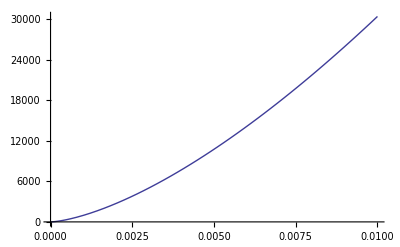

```mathematica
Plot[Force[z,0.15,(1-0.4^2)/(0.5*10^8),(1-0.25^2)/(5*10^9)],{z,0,0.01}]
```

```mathematica
20000
```

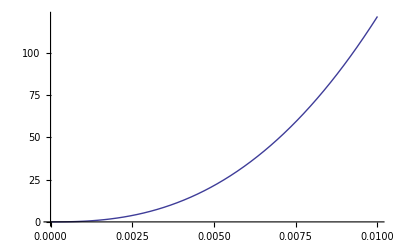

```mathematica
Plot[Pot[z,0.15,(1-0.4^2)/(0.5*10^8),(1-0.25^2)/(5*10^9)],{z,0,0.01}]
```

```mathematica
hhertz[M1_,U1_,R1_,X1_,X2_]:=(15*M1*U1^2(X1+X2)/(16 R1^(1/2)))^(2/5)
thertz[M1_,U1_,R1_,X1_,X2_]:=2.9432(15 M1 (X1+X2) / (16 R1^(1/2)))^(2/5)U1^(-1/5)
```

```mathematica
hhertz[7,1,0.15,(1-0.4^2)/(1.0*10^7),(1-0.25^2)/(5*10^9)]
thertz[7,1,0.15,(1-0.4^2)/(1.0*10^7),(1-0.25^2)/(5*10^9)]
```

0.0045889

0.013506

```mathematica
0.007*1
```

0.007

```mathematica
Solve[Force[z,0.15,(1-0.4^2)/(1.0*10^7),(1-0.25^2)/(5*10^9)]==70,z]
```

{{z→0.000506883}}

```mathematica
1/√2//N
```

```mathematica
0.7071067811865475
```

0.707107

```mathematica
Cos[0.1/2]
```

0.99875

```mathematica
1-0.99875
```

```mathematica
0.0012499999999999734
```

```mathematica
Sin[0.1/2]
```

0.0499792

```mathematica
Rotate
```

```mathematica
dt = 1;
oc = {1.0,0.0,0.0};
po0 ={0.,1.,0.};
vo0 = {0.0,0.0,0.1};
ao0 = 0.0;
avo0 = {0.0,0.5,0.0};
avo0N = Norm[avo0];

nowcoords1 = {po0 ,po0 + RotationMatrix[ao0,avo0/avo0N].oc}
nextcoords1= {po0 + vo0 * dt,po0 + vo0 * dt + RotationMatrix[(ao0+avo0N*dt),avo0/avo0N].oc} 
nowcoords2 = {nowcoords1[[2]]-RotationMatrix[ao0,avo0].oc,nowcoords1[[2]]}
nextcoords2 = {nowcoords1[[2]]-RotationMatrix[ao0,avo0].oc,nowcoords1[[2]]}
```

{{0.,1.,0.},{1.,1.,0.}}

{{0.,1.,0.1},{0.877583,1.,-0.379426}}

{{0.,1.,0.},{1.,1.,0.}}

{{0.,1.,0.},{1.,1.,0.}}

```mathematica
nowvel = {vo0 , vo0 + RotationMatrix[ao0,avo0].Cross[avo0,oc]}
nextcom = nowcoords1[[2]]+nowvel[[2]]*dt
```

{{0.,0.,0.1},{0.,0.,-0.4}}

{1.,1.,-0.4}

```mathematica
mass =1;
abc = {2.0,0.5,1.0};
intens={{1/12 mass(abc[[2]]^2+abc[[3]]^2),0,0},{0,1/12 mass(abc[[1]]^2+abc[[3]]^2),0},{0,0,1/12 mass(abc[[1]]^2+abc[[2]]^2)}};
intens // TableForm
```

0.104167 | 0 | 0
0 | 0.416667 | 0
0 | 0 | 0.354167

```mathematica
intenso[intens_,m_,d_,dir_]:= Table[If[(it1==it2) && it1!=dir,intens[[it1,it2]]+m*d^2,intens[[it1,it2]]],{it1,1,3},{it2,1,3}]
intensO=intenso[intens,mass,1,1];
intensO // TableForm
```

0.104167 | 0 | 0
0 | 1.41667 | 0
0 | 0 | 1.35417

```mathematica
l1=intensO.avo0
l2=intensO.avo0 -Cross[oc,mass*nowvel[[2]]]
l3=intens.(avo0*0.30833333333333324/0.20833333333333331)
```

{0.,0.708333,0.}

{0.,0.308333,0.}

{0.,0.308333,0.}

```mathematica
(l1.l1)/(1.4166666666666665*2)
```

0.177083

```mathematica
(l2.l2)/(0.41666666666666663*2)
```

0.114083

```mathematica
0.30833333333333324/0.20833333333333331
```

1.48

```mathematica
1/2 avo0.(intensO.avo0)
```

0.177083

```mathematica
1/2(avo0).(intens.(avo0))
```

0.0520833

```mathematica
1/2(avo0*1.4799999999999998).(intens.(avo0*1.4799999999999998))
```

0.114083

```mathematica
Graphics3D[{Arrow[{{0.,0.,0.},nowcoords1[[1]],nowcoords1[[2]]}],
Arrow[{{0.,0.,0.},nextcoords1[[1]],nextcoords1[[2]]}]}]
```

-Graphics3D-

```mathematica
bigmatprod[bigmat_,bigvec_]:={bigmat[[1,1]].bigvec[[1]] + bigmat[[1,2]].bigvec[[2]] ,bigmat[[2,1]].bigvec[[1]] +bigmat[[2,2]].bigvec[[2]]}
```

```mathematica
cmat= {{0,-cz,cy},{cz,0,-cx},{-cy,cx,0}};
cmat//TableForm
mmat ={ {m,0,0},{0,m,0},{0,0,m}};
mmat // TableForm
nullmat = {{0,0,0},{0,0,0},{0,0,0}};
i0mat = {{I0xx,0,0},{0,I0yy,0},{0,0,I0zz}};
i0mat //TableForm
accmat = {{ax,ay,az},{αx,αy,αz}};
accmat //TableForm
ω = {ωx,ωy,ωz};
vcm = {vx,vy,vz};
cm = {cx,cy,cz};
```

0 | -cz | cy
cz | 0 | -cx
-cy | cx | 0

m | 0 | 0
0 | m | 0
0 | 0 | m

I0xx | 0 | 0
0 | I0yy | 0
0 | 0 | I0zz

ax | ay | az
αx | αy | αz

```mathematica
{mmat,-m*cmat}
```

{{{m,0,0},{0,m,0},{0,0,m}},{{0,cz m,-cy m},{-cz m,0,cx m},{cy m,-cx m,0}}}

```mathematica
cmat.cmat
```

{{-cy^2-cz^2,cx cy,cx cz},{cx cy,-cx^2-cz^2,cy cz},{cx cz,cy cz,-cx^2-cy^2}}

```mathematica
{{mmat,-m*cmat},{m*cmat,i0mat-m*(cmat.cmat)}}.accmat
```

Dot::dotsh: Tensors {{{{m, 0, 0}, {0, m, 0}, {0, 0, m}}, {{0, cz\ m, -cy\ m}, {-cz\ m, 0, cx\ m}, {cy\ m, -cx\ m, 0}}}, {{{0, -cz\ m, cy\ m}, {cz\ m, 0, -cx\ m}, {-cy\ m, cx\ m, 0}}, {{I0xx - (Times[« 2 »] + Times[« 2 »])\ m, -cx\ cy\ m, -cx\ cz\ m}, {-cx\ cy\ m, I0yy - (Times[« 2 »] + Times[« 2 »])\ m, -cy\ cz\ m}, {-cx\ cz\ m, -cy\ cz\ m, I0zz - (Times[« 2 »] + Times[« 2 »])\ m}}}} and {{ax, ay, az}, {αx, αy, αz}} have incompatible shapes.

{{{{m,0,0},{0,m,0},{0,0,m}},{{0,cz m,-cy m},{-cz m,0,cx m},{cy m,-cx m,0}}},{{{0,-cz m,cy m},{cz m,0,-cx m},{-cy m,cx m,0}},{{I0xx-(-cy^2-cz^2) m,-cx cy m,-cx cz m},{-cx cy m,I0yy-(-cx^2-cz^2) m,-cy cz m},{-cx cz m,-cy cz m,I0zz-(-cx^2-cy^2) m}}}}.{{ax,ay,az},{αx,αy,αz}}

```mathematica
{{mmat,-m*cmat},{m*cmat,i0mat-m*(cmat.cmat)}}//TableForm
```

m | 0 | 0
0 | m | 0
0 | 0 | m | 0 | cz m | -cy m
-cz m | 0 | cx m
cy m | -cx m | 0
0 | -cz m | cy m
cz m | 0 | -cx m
-cy m | cx m | 0 | I0xx-(-cy^2-cz^2) m | -cx cy m | -cx cz m
-cx cy m | I0yy-(-cx^2-cz^2) m | -cy cz m
-cx cz m | -cy cz m | I0zz-(-cx^2-cy^2) m

```mathematica
lhs={{Fx,Fy,Fz},{Tx,Ty,Tz}} ;
rhs=bigmatprod[{{mmat,-m*cmat},{m*cmat,i0mat-m*(cmat.cmat)}},accmat] + {m*Cross[ω,Cross[ω,cm]],Cross[ω,(i0mat-m*(cmat.cmat)).ω]};
lhs//TableForm
rhs/.{cx->0,cz->0,cy->0}//TableForm
```

Fx | Fy | Fz
Tx | Ty | Tz

ax m | ay m | az m
I0xx αx-I0yy ωy ωz+I0zz ωy ωz | I0yy αy+I0xx ωx ωz-I0zz ωx ωz | I0zz αz-I0xx ωx ωy+I0yy ωx ωy

```mathematica
{{mat1,mat2},{mat3,mat4}}//TableForm
```

1 | 0 | 0
1 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0
1 | 0 | 0
1 | 0 | 0
1 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0
1 | 0 | 0

```mathematica
{{mat111,mat112,mat113,mat211,mat212,mat213},{mat121,mat122,mat123,mat221,mat222,mat223},
```

```mathematica
mat1={{1,0,0},{0,1,0},{0,0,1}}
mat2=mat1;
mat3=mat1;
mat4=mat1;
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
vec1={1.,1.,1.};
vec2={1.,1.,1.};
```

```mathematica
{{1,1,1}}//MatrixForm
```

(1 | 1 | 1)

```mathematica
vec1//MatrixForm
```

(1. | 1. | 1.)

```mathematica
{{mat1,mat2},{mat3,mat4}}//TableForm
{{mat1,mat2},{mat3,mat4}}.{vec1,vec2}//TableForm
```

1 | 0 | 0
0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
1 | 0 | 0
0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1

Dot::dotsh: Tensors {{{{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}, {{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}}, {{{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}, {{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}}} and {{1., 1., 1.}, {1., 1., 1.}} have incompatible shapes.

{{{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,1}}},{{{1,0,0},{0,1,0},{0,0,1}},{{1,0,0},{0,1,0},{0,0,1}}}}.{{1.,1.,1.},{1.,1.,1.}}

```mathematica
matmat
```

```mathematica
bigmatprod[bigmat_,bigvec_]:={bigmat[[1,1]].bigvec[[1]] + bigmat[[1,2]].bigvec[[2]] ,bigmat[[2,1]].bigvec[[1]] +bigmat[[2,2]].bigvec[[2]]}
```

```mathematica
bigmatprod[{{mat1,mat2},{mat3,mat4}},{vec1,vec2}]//TableForm
```

2. | 2. | 2.
2. | 2. | 2.

```mathematica
{mat1.vec1 + mat2.vec2}
```